```mathematica
ClearAll["Global`*"];
```

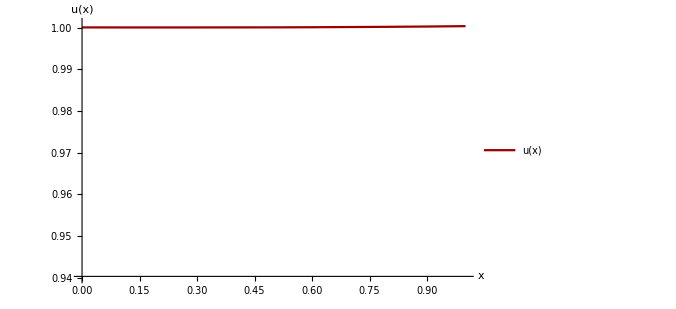

```mathematica
SetDirectory[NotebookDirectory[]];
Y=Import["sol.txt","Data"];pic1=ListLinePlot[Y,AxesStyle->Thick,PlotStyle->{Darker[Red,0.4],Thick},PlotLegends->{"u(x)"},LabelStyle->Directive[20],AxesLabel->{"x","u(x)"},ImageSize->500,PlotRange->{0.94,1.001}]
```

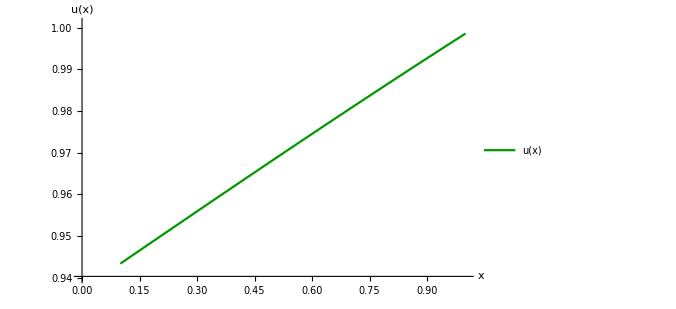

```mathematica
SetDirectory[NotebookDirectory[]];
Y=Import["sol.txt","Data"];pic2=ListLinePlot[Y,AxesStyle->Thick,PlotStyle->{Darker[Green,0.4],Thick},PlotLegends->{"u(x)"},LabelStyle->Directive[20],AxesLabel->{"x","u(x)"},ImageSize->500,PlotRange->{0.94,1.001}]
```

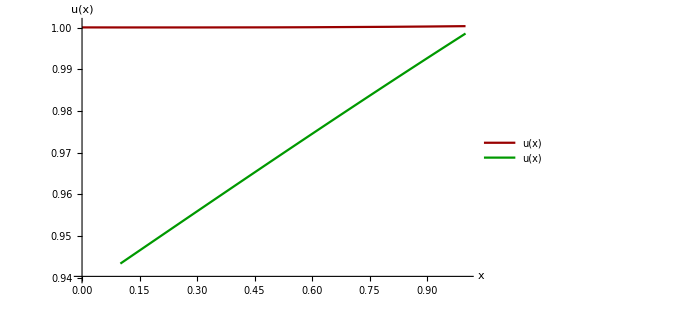

```mathematica
Show[pic1,pic2]
```

```mathematica
Integrate[E^x Sin[Pi x],{x,0,1}]
```

((1+ⅇ) π)/(1+π^2)

```mathematica
FullSimplify[Integrate[E^x(Sin[Pi x]-(x(1+E)Pi)/(2(1+Pi^2))),{x,0,1}]x+Sin[Pi x]-(x(1+E)Pi)/(2(1+Pi^2))]
```

Sin[π x]

```mathematica
N[Pi,20]
```

3.1415926535897932385

```mathematica
ClearAll["Global`*"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
G=Import["sol_SINGL.txt","Data"];
pic=ListPointPlot3D[G,PlotStyle->{Purple},LabelStyle->Directive[20],PlotLegends->{"γ(r)"},AxesLabel->(Style[#,17,Bold,Italic]&/@{"x","y","γ(r)"}),LabelStyle->Directive[15],AxesStyle->Thick,BoxRatios->{1,1,0.6},PlotRange->All,ImageSize->500,ViewPoint->{Pi,Pi/2,1},Boxed->False]
```

-Graphics3D-

```mathematica
Export["part2.pdf",pic];
```

```mathematica
0.000367309/0.0000917545
```

4.00317

```mathematica
0.0000917545/(2.29341 10^-5)
```

4.00079

```mathematica
3.67309 10^-4
```

0.000367309

```mathematica
9.17544/2.2934
```

4.0008

```mathematica
36.7309/9.17544
```

4.00318

```mathematica
0.000368791/(9.31712 10^-5)
```

3.95821

```mathematica
9.31712/2.43345
```

3.82877